# 用轮廓线制作手绘图

```mathematica
contourFourierDescriptors[Line[contour_],n_]:=Module[{z,k},z=Fourier[Complex@@@contour];
k=Max[Ceiling[1/2 Min[Length[contour]/2,n]],1];
z[[k;;-k]]=0;
z]
```

```mathematica
reconstructContour[descriptors_]:=Module[{rc},rc=ReIm[InverseFourier[descriptors]];
Line[Append[rc,rc[[1]]]]]
```

```mathematica
smoothContour[contour_, n_] := 
 reconstructContour[contourFourierDescriptors[contour, n]]
```

```mathematica
img = -Graphics-;
```

```mathematica
(cs=Join@@Values[ComponentMeasurements[Binarize[ColorNegate[img]],"Contours"]])//RandomChoice
```

Line[{{132,96},{132,96},{133,96},{133,96},{133,95},{133,95},{132,95},{132,95},{132,96}}]

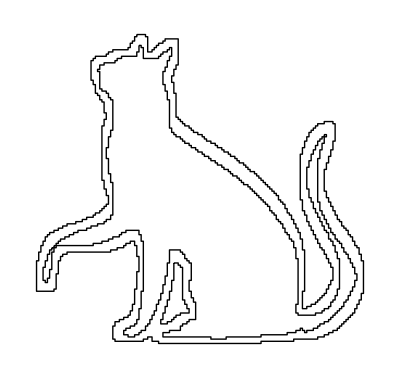

```mathematica
Graphics[cs]
```

```mathematica
Table[HighlightImage[img,{AbsoluteThickness[3],smoothContour[cs[[2]],n]},PlotRangePadding->10],{n,{3,5,9,11,21,∞}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
car = -Graphics-; mask = -Graphics-;
```

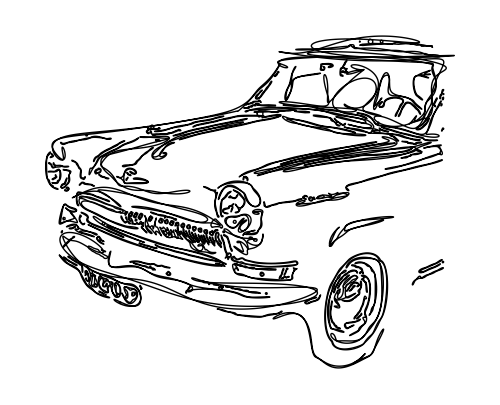

```mathematica
contours=ImageMeasurements[EdgeDetect[Blur[ImageMultiply[car,mask],2],1],"Contours"];
Graphics[smoothContour[#,21]&/@contours,ImageSize->500]
```

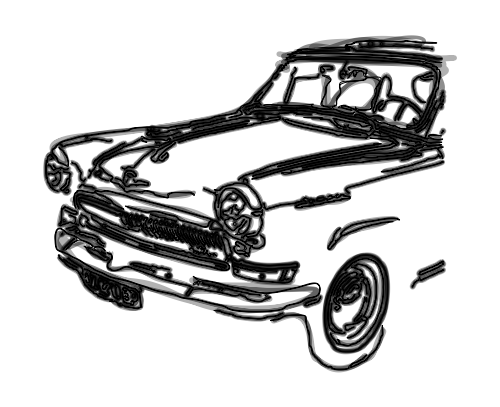

```mathematica
Graphics[Table[{GrayLevel[0,n/70],AbsoluteThickness[80/n],(reconstructContour[contourFourierDescriptors[#1,n]]&)/@contours},{n,{21,31,111}}],ImageSize->500]
```

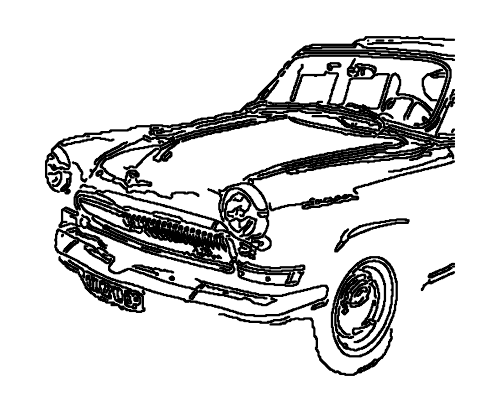

```mathematica
contours=ImageMeasurements[EdgeDetect[Blur[ImageMultiply[car,mask],2],1],"Contours"];
Graphics[contours,ImageSize->500]
```